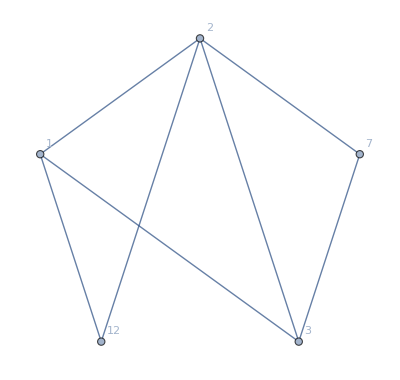
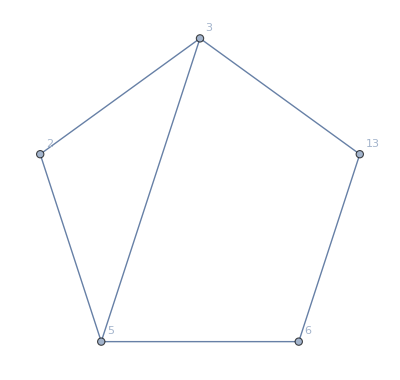
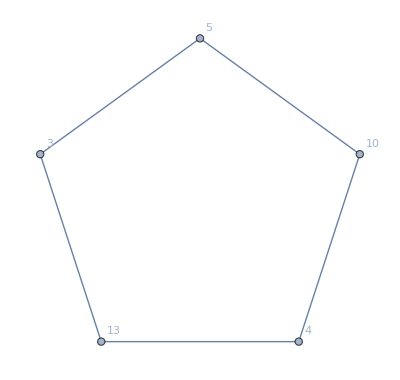
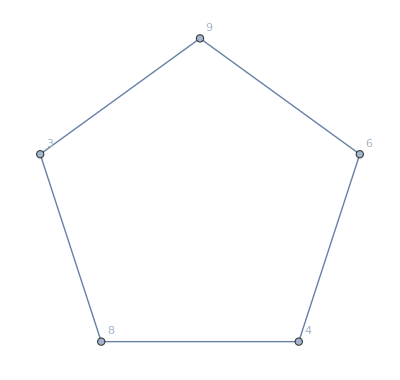
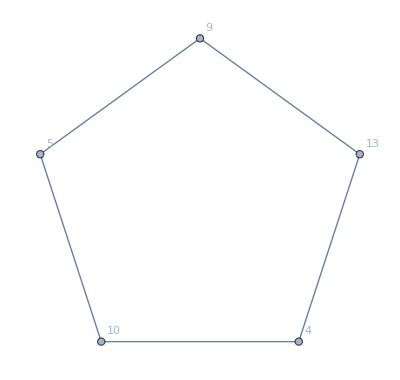
{{{1,2,3,12,7},-Graphics-,7},{{2,3,5,13,6},-Graphics-,6},{{3,5,13,4,10},-Graphics-,5},{{3,9,8,4,6},-Graphics-,5},{{5,9,13,4,10},-Graphics-,5}}

```mathematica
With[{k=10087},
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{adj,Graph[h,GraphLayout->"CircularEmbedding",VertexLabels->"Name"],EdgeCount[h]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==5&]}
]

]
]
```

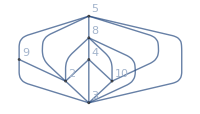
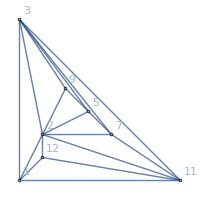
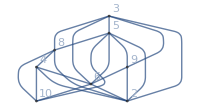
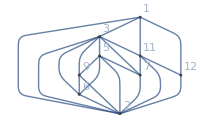
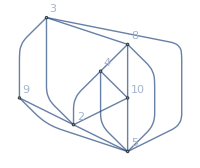
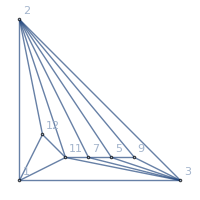
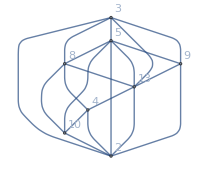
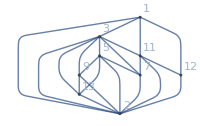
-Graphics-{(-3+x)^2 (-2+x) (13-7 x+x^2),24} | -Graphics-{(-3+x)^5 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^2 (-2+x) (15-7 x+x^2),0} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0}
-Graphics-{(-3+x)^2 (-2+x) (10-6 x+x^2),48} | -Graphics-{(-3+x)^5 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^2 (-2+x) (15-7 x+x^2),0} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0}
-Graphics-{(-4+x) (-3+x)^2 (-2+x)^2,0} | -Graphics-{(-3+x)^5 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^2 (-2+x) (13-7 x+x^2),0} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0}
-Graphics-{(-4+x) (-3+x)^2 (-2+x) (10-6 x+x^2),0} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0}
-Graphics-{(-5+x) (-4+x) (-3+x)^2 (-2+x) (15-7 x+x^2),0} | -Graphics-{(-5+x) (-4+x) (-3+x)^5 (-2+x),0}6

```mathematica
With [{g=ReadGrof[10087],border={2,3,5,13,6}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

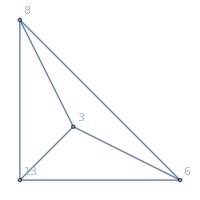
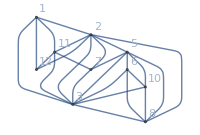
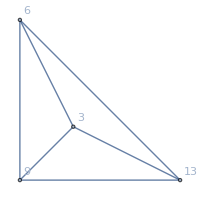
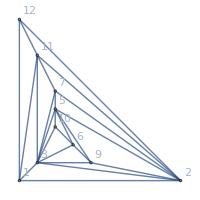
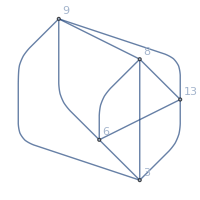
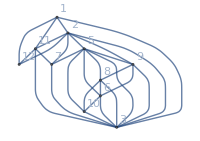
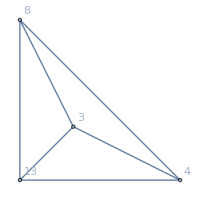
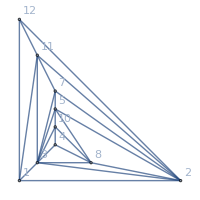
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (10-6 x+x^2),48}
-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x) (17-8 x+x^2),0}5

```mathematica
With [{g=ReadGrof[10087],border={3,9,8,4,6}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

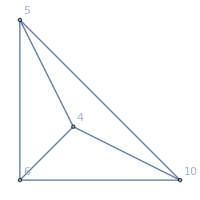
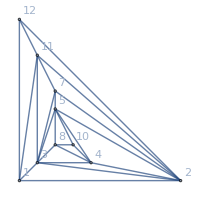
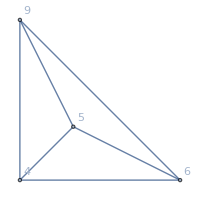
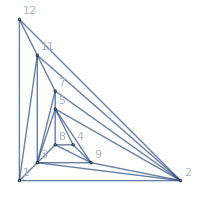
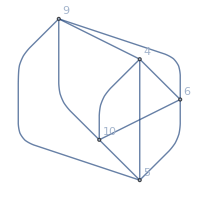
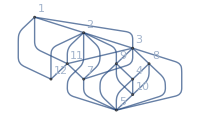
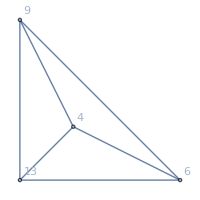
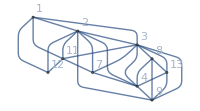
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (10-6 x+x^2),48}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24}
-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x) (17-8 x+x^2),0}5

```mathematica
With [{g=ReadGrof[10087],border={5,9,13,4,10}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

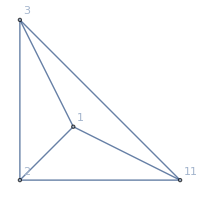
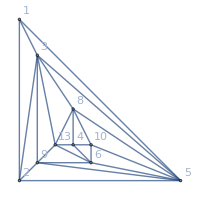
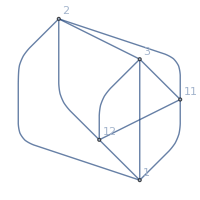
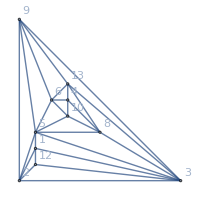
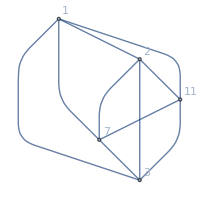
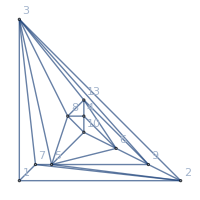
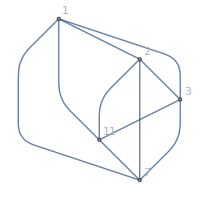
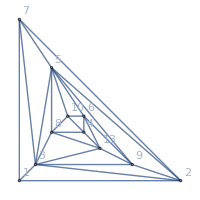
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^3 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72}
-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),0}7

```mathematica
With [{g=ReadGrof[10087],border={1,2,3,12,7}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

```mathematica
Table[
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{k,Grid[{adj},Frame->All],Graph[h,GraphLayout->"CircularEmbedding",VertexLabels->"Name",ImageSize->40],Style[EdgeCount[h],Red]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==5&]}
]
],
{k,20000,20050}]
```

{{{20000,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20000,9 | 6 | 4 | 10 | 13,-Graphics-,5},{20000,5 | 9 | 8 | 10 | 12,-Graphics-,5}},{{20001,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20001,2 | 3 | 5 | 6 | 12,-Graphics-,6}},{{20002,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20002,9 | 6 | 8 | 10 | 13,-Graphics-,6}},{{20003,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20003,2 | 3 | 5 | 6 | 12,-Graphics-,6}},{{20004,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20004,2 | 3 | 5 | 6 | 12,-Graphics-,6},{20004,6 | 8 | 4 | 12 | 13,-Graphics-,7}},{{20005,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20005,2 | 3 | 5 | 6 | 12,-Graphics-,6},{20005,6 | 8 | 4 | 12 | 13,-Graphics-,7}},{{20006,1 | 3 | 7 | 5 | 9,-Graphics-,7}},{{20007,1 | 3 | 7 | 5 | 9,-Graphics-,7}},{{20008,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20008,2 | 3 | 5 | 6 | 12,-Graphics-,6},{20008,6 | 8 | 4 | 10 | 12,-Graphics-,7}},{{20009,2 | 3 | 9 | 11 | 13,-Graphics-,7},{20009,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20010,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20011,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20012,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20013,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20014,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20015,3 | 5 | 6 | 4 | 10,-Graphics-,7},{20015,5 | 6 | 8 | 4 | 13,-Graphics-,7}},{{20016,5 | 6 | 8 | 4 | 13,-Graphics-,7}},{{20017,2 | 3 | 9 | 13 | 11,-Graphics-,7},{20017,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20018,2 | 3 | 9 | 13 | 11,-Graphics-,7},{20018,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20019,1 | 3 | 13 | 9 | 12,-Graphics-,6},{20019,1 | 2 | 7 | 9 | 5,-Graphics-,5},{20019,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20020,1 | 2 | 3 | 13 | 5,-Graphics-,6},{20020,2 | 7 | 9 | 5 | 6,-Graphics-,5},{20020,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20021,2 | 3 | 7 | 5 | 8,-Graphics-,6}},{{20022,1 | 3 | 7 | 5 | 8,-Graphics-,5}},{{20023,2 | 3 | 7 | 9 | 5,-Graphics-,7},{20023,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20024,1 | 2 | 3 | 5 | 13,-Graphics-,6},{20024,3 | 6 | 13 | 4 | 10,-Graphics-,6},{20024,3 | 7 | 5 | 8 | 10,-Graphics-,5},{20024,5 | 6 | 8 | 13 | 4,-Graphics-,6}},{{20025,3 | 5 | 9 | 6 | 8,-Graphics-,7},{20025,5 | 13 | 4 | 6 | 10,-Graphics-,7}},{{20026,3 | 6 | 13 | 4 | 10,-Graphics-,7},{20026,3 | 5 | 6 | 8 | 10,-Graphics-,7}},{{20027,3 | 5 | 9 | 8 | 6,-Graphics-,7},{20027,5 | 8 | 13 | 4 | 10,-Graphics-,7}},{{20028,3 | 5 | 9 | 13 | 10,-Graphics-,6},{20028,3 | 5 | 13 | 4 | 10,-Graphics-,6},{20028,3 | 6 | 8 | 4 | 10,-Graphics-,6},{20028,5 | 6 | 8 | 13 | 4,-Graphics-,6}},{{20029,3 | 5 | 13 | 4 | 10,-Graphics-,5},{20029,3 | 9 | 8 | 4 | 6,-Graphics-,5},{20029,5 | 9 | 13 | 4 | 10,-Graphics-,5}},{{20030,2 | 3 | 12 | 13 | 11,-Graphics-,7},{20030,2 | 3 | 5 | 9 | 6,-Graphics-,7},{20030,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20031,2 | 5 | 9 | 6 | 10,-Graphics-,5},{20031,3 | 5 | 6 | 4 | 10,-Graphics-,6},{20031,5 | 13 | 6 | 8 | 4,-Graphics-,6}},{{20032,5 | 9 | 6 | 8 | 10,-Graphics-,6}},{{20033,2 | 3 | 9 | 12 | 11,-Graphics-,7},{20033,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20034,2 | 3 | 9 | 11 | 13,-Graphics-,7},{20034,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20035,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20036,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20037,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20038,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20039,3 | 5 | 6 | 4 | 10,-Graphics-,7},{20039,5 | 6 | 8 | 4 | 13,-Graphics-,7}},{{20040,5 | 6 | 8 | 4 | 13,-Graphics-,7}},{{20041,2 | 3 | 9 | 11 | 13,-Graphics-,7},{20041,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20042,2 | 3 | 7 | 5 | 8,-Graphics-,6}},{{20043,1 | 3 | 7 | 5 | 8,-Graphics-,5}},{{20044,1 | 2 | 3 | 5 | 13,-Graphics-,6},{20044,3 | 6 | 13 | 4 | 10,-Graphics-,6},{20044,3 | 7 | 5 | 8 | 10,-Graphics-,5},{20044,5 | 6 | 8 | 13 | 4,-Graphics-,6}},{{20045,3 | 5 | 9 | 6 | 8,-Graphics-,7},{20045,5 | 13 | 4 | 6 | 10,-Graphics-,7}},{{20046,3 | 6 | 13 | 4 | 10,-Graphics-,7},{20046,3 | 5 | 6 | 8 | 10,-Graphics-,7}},{{20047,3 | 5 | 9 | 8 | 6,-Graphics-,7},{20047,5 | 8 | 13 | 4 | 10,-Graphics-,7}},{{20048,3 | 5 | 9 | 13 | 10,-Graphics-,6},{20048,3 | 5 | 13 | 4 | 10,-Graphics-,6},{20048,3 | 6 | 8 | 4 | 10,-Graphics-,6},{20048,5 | 6 | 8 | 13 | 4,-Graphics-,6}},{{20049,3 | 5 | 13 | 4 | 10,-Graphics-,5},{20049,3 | 9 | 8 | 4 | 6,-Graphics-,5},{20049,5 | 9 | 13 | 4 | 10,-Graphics-,5}},{{20050,2 | 3 | 11 | 12 | 13,-Graphics-,7},{20050,2 | 3 | 5 | 9 | 6,-Graphics-,7},{20050,3 | 5 | 6 | 4 | 10,-Graphics-,7}}}

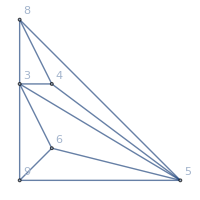
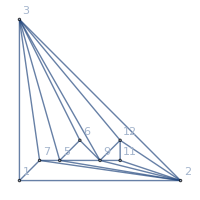
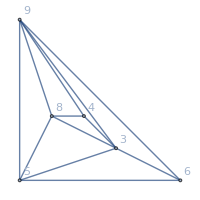
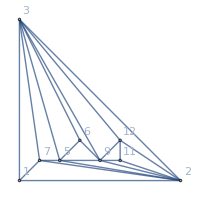
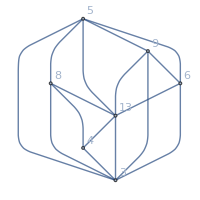
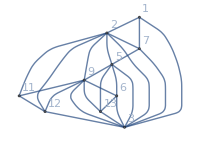
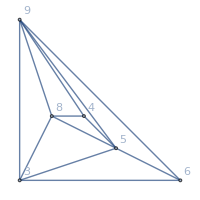
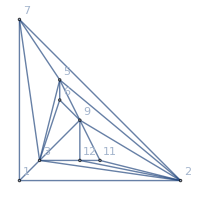
-Graphics-{(-3+x)^2 (-2+x)^2,48} | -Graphics-{(-3+x)^6 (-2+x),24}
-Graphics-{(-3+x)^3 (-2+x),24} | -Graphics-{(-3+x)^6 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-3+x)^3 (-2+x),24} | -Graphics-{(-3+x)^6 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x)^2 (-3+x)^2 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x)^2 (-3+x)^2 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-5+x) (-4+x)^2 (-3+x)^2 (-2+x),0} | -Graphics-{(-5+x) (-4+x) (-3+x)^6 (-2+x),0}6

```mathematica
With [{g=ReadGrof[20048],border={3,5,9,13,10}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

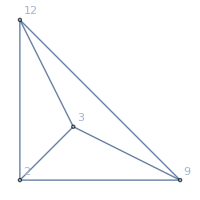
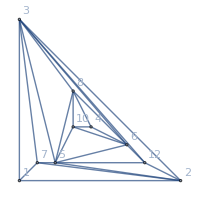
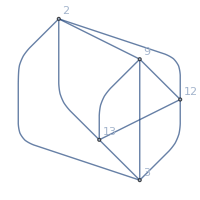
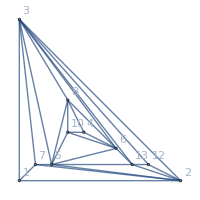
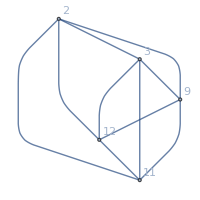
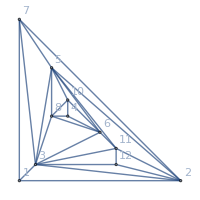
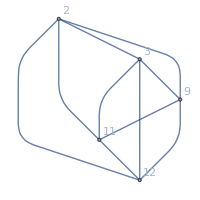
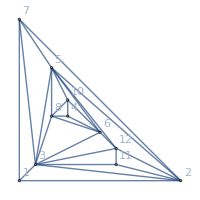
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^8 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^8 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^8 (-2+x),24}
-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x)^8 (-2+x),0}7

```mathematica
With [{g=ReadGrof[20050],border={2,3,11,12,13}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

```mathematica
With [{g=ReadGrof[20049],border={3,5,13,4,10}},
{EdgeCount[Subgraph[g,border]],Length[Select[Map[#[[1]]*#[[2]]&,Map[{ChromaticPolynomial[#[[2]][[1]],4],ChromaticPolynomial[#[[3]][[1]],4]}&,ZykovDecomposition23[g,border]]],#≠0&]]}
]
```

{5,3}